```mathematica
PerfectDistanceQ[G_]:=(Union@*Flatten@*Round@GraphDistanceMatrix[G] == Range[0,Binomial[VertexCount[G],2]]);

EdgeWeights[G_]:=AnnotationValue[G,EdgeWeight];

NoNewVertex[G_]:=Complement[(#1<->#2&@@@Subsets[VertexList[G],{2}]),EdgeList[G]]
OneNewVertex[G_]:=#<->(VertexCount[G]+1)&/@ VertexList[G]
TwoNewVertex[G_]:={(VertexCount[G]+1)<->(VertexCount[G]+2)}
NewEdges[G_]:=Join[NoNewVertex[G],OneNewVertex[G],TwoNewVertex[G]];
NextWeight[G_]:=
Module[{distances,nextWeight},
distances =DeleteCases[Union@*Flatten@*Round@*GraphDistanceMatrix@*Graph@G,0];nextWeight = Max[EdgeWeights[G]]+1;While[(nextWeight<=Length[distances])∧(distances[[nextWeight]]==nextWeight),nextWeight++];
nextWeight
]

AddWeightedEdge[G_,e_,w_]:=Graph[EdgeAdd[G,e],EdgeWeight->Append[EdgeWeights[G],w]]

Children[G_]:=AddWeightedEdge[G,#,NextWeight[G]]&/@NewEdges[G];
```

$Aborted

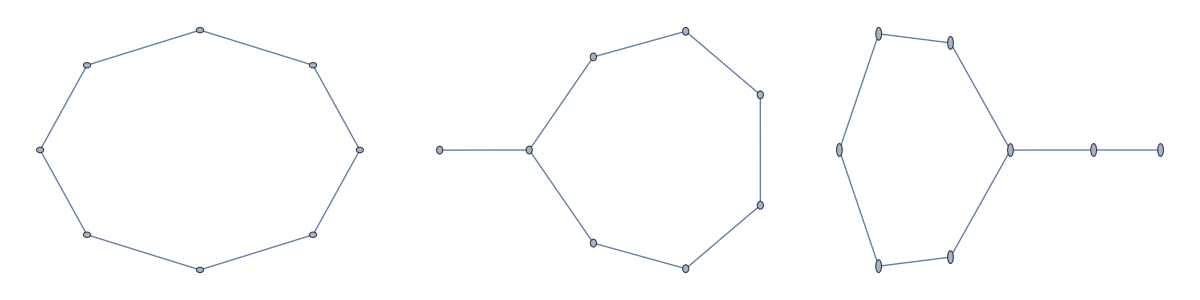
Time To Compute:	00:04:17TimeObject[{0,4,17.053},Instant] and 52.993ms
Almost Minimal Perfect Distance Graphs(3): 
-Graphics-

```mathematica
n =8;
maxEdgeCount = n;

(*TODO: Make GoodChildQ account for labelings that "obviously" cannot lead to a PDG. ie) 2 distances of length m where next weight is >= m.*)
GoodChildQ[G_]:=(VertexCount[G] <=n) ∧(SubsetQ[Range[Binomial[n,2]],EdgeWeights[G]])∧(AllTrue[First/@Select[Tally@DeleteCases[Flatten@GraphDistanceMatrix[G],0.],Last[#]>2&],NextWeight[G]<=#&])∧(Not[AnyTrue[PDGs,IsomorphicSubgraphQ[#,CanonicalGraph[G]]&]]);

PDGs = {};
stack =CreateDataStructure["Stack"];
Gstart = Graph[{1<->2},EdgeWeight->{1<->2->1}];

stack["Push",Gstart];

stack2 = CreateDataStructure["Stack"];

TotalTime = AbsoluteTiming[
(*Depth First Search*)
Until[stack["EmptyQ"]∧stack2["EmptyQ"],
G = stack["Pop"];

If[EdgeCount[G]>maxEdgeCount  ,stack2["Push",G],
If[(VertexCount[G]==n ∧ PerfectDistanceQ[G]),
AppendTo[PDGs,CanonicalGraph[G]];
,(*Else*)
children =DeleteDuplicates[Select[Children[G],GoodChildQ],LineGraph[#1]==LineGraph[#2]&&IsomorphicGraphQ[#1,#2]&];
stack["PushList",children];
];
];

If[stack["EmptyQ"],
While[Not[stack2["EmptyQ"]],
g = stack2["Pop"];
If[(Not[AnyTrue[PDGs,IsomorphicSubgraphQ[#,g]&]]),
stack["Push",g]
];
];
maxEdgeCount = maxEdgeCount+1;
];
]

][[1]];
Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Almost Minimal Perfect Distance Graphs(",Length[PDGs],"): \n",TableForm[PDGs,TableDirections->Row],"\n"
]
```